Set::setraw: Cannot assign to raw object 0.

Set::setraw: Cannot assign to raw object 1.31607.

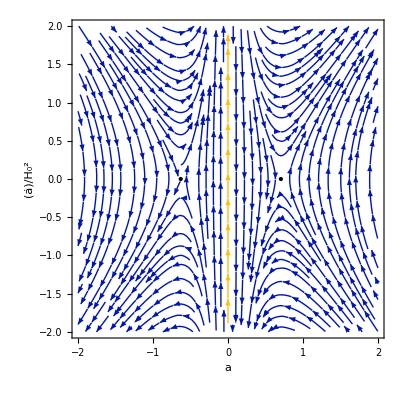

```mathematica
ClearAll[c1,c2,c3,c4,x,myvars,f,sols,sols2]
c1=0;
c2=0.15;
c3=0.1;
c4=0.75;
c5=0;
f[x_]=-(2*c2)/x^3-c3/x^2+2*c4*x;
sols=NSolve[f[x]==0,x,Reals];
sols2=Select[x/. sols,Im[#]==0&];
myvars=Array[vars,Length@sols2];
Evaluate@myvars=sols2;
SubPlus[λ]=Simplify[Sqrt[4*f'[sols2]]];
SubMinus[λ]=-1*Simplify[Sqrt[4*f'[sols2]]];
StreamPlot[{y-c5,f[x]},{x,-2,2},{y,-2,2},StreamPoints->Fine,AspectRatio->1,Epilog->{PointSize[Large],(Point[{#,c5}]&)/@(sols2)},
FrameLabel->{"a",OverDot["a"]/"H_0^2"}]
```